```mathematica
SetDirectory["/home/elyrae/Programs/Parallel/openmp/helmholtz/build"]
```

/home/elyrae/Programs/Parallel/openmp/helmholtz/build

```mathematica
data=Import["out.txt","Table"]//Flatten;
```

```mathematica
sol[x_,y_]:=x(1-x)Sin[π y];

data=Import["out.txt","Table"];
error={#⟦1⟧,#⟦2⟧,Abs[sol[#⟦1⟧,#⟦2⟧]-#⟦3⟧]}&/@data
```

{{iter,1:,Abs[-0.000139419+(1-iter) iter Sin[1: π]]},{iter,2:,Abs[-0.000139352+(1-iter) iter Sin[2: π]]},{iter,3:,Abs[-0.000139285+(1-iter) iter Sin[3: π]]},{iter,4:,Abs[-0.000139218+(1-iter) iter Sin[4: π]]},493,{iter,498:,Abs[-0.000109274+(1-iter) iter Sin[498: π]]},{iter,499:,Abs[-0.000109219+(1-iter) iter Sin[499: π]]},{iter,500:,Abs[-0.000109163+(1-iter) iter Sin[500: π]]},{max,error,Abs[-=+(1-max) max Sin[error π]]}}
 |  |  |  |

```mathematica
Subdivide[2]
```

{0,1/2,1}

```mathematica
data
```

{0.000568604,0.000567483,0.000566364,0.000565247,0.000564133,0.00056302,0.000561909,0.000560801,0.000559694,0.000558589,0.000557487,0.000556386,0.000555287,0.000554191,0.000553096,0.000552004,0.000550913,0.000549825,0.000548738,0.000547654,0.000546571,0.00054549,0.000544412,0.000543335,0.00054226,0.000541188,0.000540117,0.000539048,0.000537982,0.000536917,0.000535854,0.000534793,0.000533734,0.000532677,0.000531622,0.000530568,0.000529517,0.000528468,0.000527421,0.000526375,0.000525332,0.00052429,0.00052325,0.000522212,0.000521176,0.000520142,0.00051911,0.00051808,0.000517052,0.000516025,0.000515001,0.000513978,0.000512957,0.000511938,0.000510921,0.000509905,0.000508892,0.00050788,0.00050687,0.000505862,0.000504856,0.000503851,0.000502849,0.000501848,0.000500848,0.000499851,0.000498855,0.000497861,0.000496868,0.000495878,0.000494889,0.000493901,0.000492915,0.000491931,0.000490949,0.000489968,0.000488988,0.000488011,0.000487034,0.00048606,0.000485086,0.000484115,0.000483144,0.000482176,0.000481208,0.000480243,0.000479278,0.000478315,0.000477353,0.000476393,0.000475434,0.000474477,0.00047352,0.000472565,0.000471612,0.000470659,0.000469708,0.000468759,0.00046781,0.000466863,0.000465917,0.000464972,0.000464028,0.000463085,0.000462144,0.000461204,0.000460265,0.000459327,0.00045839,0.000457455,0.00045652,0.000455587,0.000454655,0.000453723,0.000452793,0.000451864,0.000450936,0.000450009,0.000449083,0.000448159,0.000447235,0.000446312,0.00044539,0.00044447,0.00044355,0.000442632,0.000441714,0.000440797,0.000439882,0.000438967,0.000438054,0.000437141,0.000436229,0.000435319,0.000434409,0.0004335,0.000432593,0.000431686,0.000430781,0.000429876,0.000428972,0.00042807,0.000427168,0.000426267,0.000425367,0.000424469,0.000423571,0.000422674,0.000421778,0.000420884,0.00041999,0.000419097,0.000418205,0.000417314,0.000416425,0.000415536,0.000414648,0.000413761,0.000412876,0.000411991,0.000411107,0.000410225,0.000409343,0.000408462,0.000407583,0.000406704,0.000405827,0.00040495,0.000404075,0.0004032,0.000402327,0.000401455,0.000400583,0.000399713,0.000398844,0.000397976,0.000397109,0.000396243,0.000395379,0.000394515,0.000393652,0.000392791,0.00039193,0.000391071,0.000390213,0.000389356,0.0003885,0.000387645,0.000386791,0.000385939,0.000385087,0.000384237,0.000383388,0.00038254,0.000381693,0.000380847,0.000380003,0.00037916,0.000378317,0.000377476,0.000376636,0.000375798,0.00037496,0.000374124,0.000373289,0.000372455,0.000371622,0.000370791,0.000369961,0.000369131,0.000368304,0.000367477,0.000366652,0.000365827,0.000365004,0.000364183,0.000363362,0.000362543,0.000361725,0.000360908,0.000360093,0.000359279,0.000358466,0.000357654,0.000356844,0.000356034,0.000355227,0.00035442,0.000353615,0.000352811,0.000352008,0.000351207,0.000350406,0.000349608,0.00034881,0.000348014,0.000347219,0.000346425,0.000345633,0.000344842,0.000344052,0.000343264,0.000342477,0.000341691,0.000340907,0.000340124,0.000339342,0.000338562,0.000337782,0.000337005,0.000336228,0.000335453,0.00033468,0.000333907,0.000333136,0.000332367,0.000331599,0.000330832,0.000330066,0.000329302,0.000328539,0.000327778,0.000327017,0.000326259,0.000325501,0.000324745,0.000323991,0.000323238,0.000322486,0.000321735,0.000320986,0.000320238,0.000319492,0.000318747,0.000318003,0.000317261,0.00031652,0.000315781,0.000315043,0.000314306,0.000313571,0.000312837,0.000312104,0.000311373,0.000310644,0.000309915,0.000309188,0.000308463,0.000307739,0.000307016,0.000306294,0.000305575,0.000304856,0.000304139,0.000303423,0.000302709,0.000301996,0.000301284,0.000300574,0.000299865,0.000299158,0.000298452,0.000297747,0.000297044,0.000296342,0.000295642,0.000294943,0.000294245,0.000293549,0.000292854,0.000292161,0.000291469,0.000290778,0.000290089,0.000289401,0.000288715,0.00028803,0.000287346,0.000286664,0.000285983,0.000285304,0.000284626,0.000283949,0.000283274,0.0002826,0.000281927,0.000281256,0.000280587,0.000279918,0.000279251,0.000278586,0.000277922,0.000277259,0.000276598,0.000275938,0.000275279,0.000274622,0.000273966,0.000273312,0.000272659,0.000272007,0.000271357,0.000270708,0.00027006,0.000269414,0.000268769,0.000268126,0.000267484,0.000266843,0.000266204,0.000265566,0.000264929,0.000264294,0.00026366,0.000263028,0.000262397,0.000261767,0.000261139,0.000260511,0.000259886,0.000259262,0.000258639,0.000258017,0.000257397,0.000256778,0.00025616,0.000255544,0.000254929,0.000254316,0.000253704,0.000253093,0.000252483,0.000251875,0.000251268,0.000250663,0.000250059,0.000249456,0.000248855,0.000248254,0.000247656,0.000247058,0.000246462,0.000245867,0.000245274,0.000244681,0.000244091,0.000243501,0.000242913,0.000242326,0.00024174,0.000241156,0.000240573,0.000239991,0.000239411,0.000238832,0.000238254,0.000237677,0.000237102,0.000236528,0.000235956,0.000235384,0.000234814,0.000234246,0.000233678,0.000233112,0.000232547,0.000231984,0.000231421,0.00023086,0.0002303,0.000229742,0.000229185,0.000228629,0.000228074,0.00022752,0.000226968,0.000226417,0.000225868,0.000225319,0.000224772,0.000224226,0.000223682,0.000223138,0.000222596,0.000222055,0.000221515,0.000220977,0.00022044,0.000219904,0.000219369,0.000218835,0.000218303,0.000217772,0.000217242,0.000216714,0.000216186,0.00021566,0.000215135,0.000214611,0.000214089,0.000213568,0.000213048,0.000212529,0.000212011,0.000211494,0.000210979,0.000210465,0.000209952,0.00020944,0.00020893,0.000208421,0.000207912,0.000207406,0.0002069,0.000206395,0.000205892,0.000205389,0.000204888,0.000204389,0.00020389,0.000203392,0.000202896,0.000202401,0.000201907,0.000201414,0.000200922,0.000200431,0.000199942,0.000199453,0.000198966,0.00019848,0.000197995,0.000197512,0.000197029,0.000196548,0.000196067,0.000195588,0.00019511,0.000194633,0.000194157,0.000193683,0.000193209,0.000192737,0.000192265,0.000191795,0.000191326,0.000190858,0.000190391,0.000189925,0.000189461,0.000188997,0.000188534,0.000188073,0.000187613,0.000187154,0.000186695,0.000186238,0.000185782,0.000185328,0.000184874}

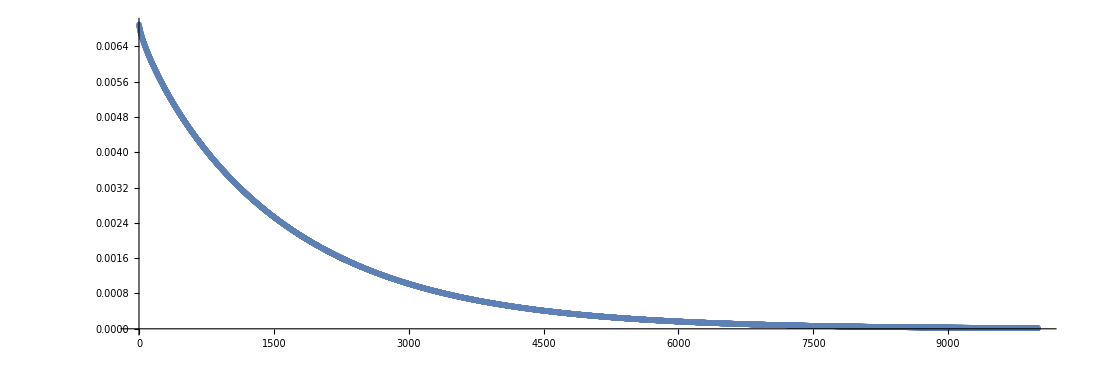

```mathematica
ListPlot[data,AspectRatio->1/3,ImageSize->1100]
```

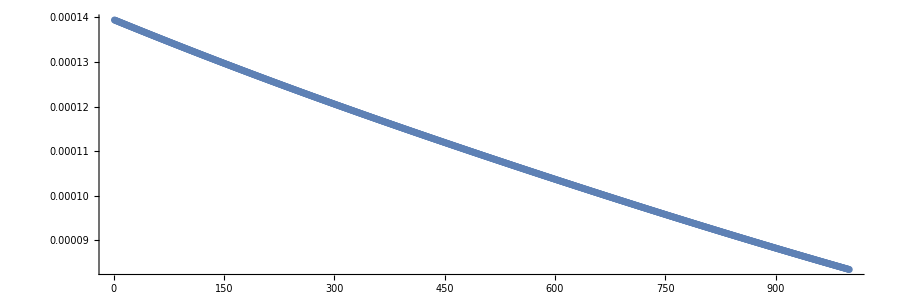

```mathematica
ListPlot[data,AspectRatio->1/3,ImageSize->900]
```

```mathematica
ListPlot3D[error]
```

-Graphics3D-

```mathematica
ListPointPlot3D[data,ImageSize->500]
```

-Graphics3D-